```mathematica
Droplets analyzer
```

```mathematica
Edit the input appearing in red if needed
```

```mathematica
SetDirectory[NotebookDirectory[]];FileNames[];
xpserie="series09"; (* input file name without the extension*)
frame = 100; (*number of frames*)
diam=12; (*diameter of the droplets used to compute the concentration*)
channelr=Atto633; (*;red dye*)
channelg=Alx488;(*green dye*)
channelo=TxRed;(*orange dye*)
channelb=CascadeBlue; (*blue dye*)
bf=4; (*input the channel number for the microscopy images, by acquisition order (bf = brightfield used for droplet segmentation)*)
chr=4;
chg=3;
cho=2;
chb=1;
nfchan=4; (*number of fluorescence channel*)
nchan=4;(*number of channels (total including bright field*)
dye={"CascB","TxRed","Alx488","Atto633"}; (*dyes in the order they have been acquired*)
theme={"blue","orange","green","red"}; (*associated theme for scheme representation: choose between "green","orange","red" and "blue*)
colhisto={RGBColor[0,0.42,0.99],Orange,Green,Red}; (*color to be associated*)
samplename={"0% H2O2", "0.3%","0.6%","1.3%","2.5%","5%"};(*names of the samples*)
sampleconc={0,0,0,0,0,0}; 

DiverseFunctions;

crop[im_]:=ImageTrim[im,{{0,0},{4000,4000}}];(* crop parameter {{x1,y1},{x2,y2}}, to work on a croped area of the images*)
fluo[im_,cent_]:=PixelValue[ImageConvolve[im,DiskMatrix[r]/Total[DiskMatrix[r]]],cent]; (*function to extract the fluorescence from a disk of radius "r"*)
resc[dat_]:=Rescale[dat,{Quantile[dat,0.01],Quantile[dat,0.99]}];(* rescaling function*)
numb[num_]:=NumberForm[100N[num],2];
pt=0.012; (*option in PointSize for the ListPlot*)
Themes`AddThemeRules["red",Frame->True,PlotStyle->Directive[Red,PointSize[pt],Opacity[0.4]], FrameStyle->Directive[RGBColor[0.3,0.3,0.3],14],Background->White, PlotLabel->Style[channel1,16,Red],FrameLabel->{"count","fluo red"}];
Themes`AddThemeRules["green",Frame->True,PlotStyle->Directive[CMYKColor[0.54,0,1,0.32],PointSize[pt],Opacity[0.4]],FrameStyle->Directive[RGBColor[0.3,0.3,0.3],14],Background->White,PlotLabel->Style[channel2,16,CMYKColor[0.54,0,1,0.32]],FrameLabel->{"count","fluo green"}];
Themes`AddThemeRules["orange",Frame->True,PlotStyle->Directive[Orange,PointSize[pt],Opacity[0.4]],FrameStyle->Directive[RGBColor[0.3,0.3,0.3],14],Background->White,PlotLabel->Style[channel3,16,Orange],FrameLabel->{"count","fluo orange"}];
Themes`AddThemeRules["blue",Frame->True,PlotStyle->Directive[Blue,PointSize[pt],Opacity[0.4]],FrameStyle->Directive[RGBColor[0.3,0.3,0.3],14],Background->White,PlotLabel->Style[channel4,16,Blue],FrameLabel->{"count","fluo blue"}];
colorall=Directive[{RGBColor[0.54,0.53,0.52],Opacity[1],EdgeForm[None]}];
colorpos=Directive[{Red,Opacity[1],EdgeForm[None]}];Themes`AddThemeRules["histo",Frame->True,FrameLabel->{"fluorescence (a.u.)","count"},FrameStyle->Directive[RGBColor[0.2,0.2,0.2],14],ChartStyle->{colorall,colorpos}];
sub[im_,min_]:=Image[MapThread[Subtract,ImageData/@{im,min}]]; (*subtract background function*)
div[im_,min_]:=Image[MapThread[Divide,ImageData/@{im,min}]];(*divide background function*)
ran[list_]:={Quantile[list,0.01]-0.1*Quantile[list,0.01],Quantile[list,0.99]+0.3*Quantile[list,0.99]}(*function to define automatically the PlotRange*)
detection[im_]:=FillingTransform[Colorize[DeleteBorderComponents[MorphologicalComponents[im]]]];
(* detection of components on defocused bright field channel*)
numlistt=Flatten[{Table["00"<>ToString[i],{i,1,9}],Table["0"<>ToString[i],{i,10,99}],Table[i,{i,100,200}]},1]; (*generate a 3 figure list for time points*)
numlistxy=Flatten[{Table["0"<>ToString[i],{i,1,9}],Table[i,{i,10,200}]},1]; (*generate a 2 figure list for XY positions*)
cloudclean[list_,cleaninglist_,thres_]:=(neardr=Nearest[cleaninglist];
nei=Drop[neardr[#,200],1]&/@cleaninglist;
allnei=Table[Median[Table[EuclideanDistance[cleaninglist[[i]],nei[[i,j]]],{j,1,9}]],{i,Length@cleaninglist}];
med=Mean[allnei];Pick[list,#<thres med&/@allnei]) (*Drop selection function (applies a nearest nearbough function for filtering out outliers)*)
SetOptions[#,Frame->True,FrameStyle->Directive[{15,Black}]]&/@{ListPlot,ListLinePlot};
```

```mathematica
Background image for field inhomogeneity correction
```

```mathematica
SetDirectory[NotebookDirectory[]];FileNames[];
backgroundim=crop/@Import["minall.tif"]; 
(*import the background images (same number and order of channels and same size*)
```

## Data extraction (fluorescence and coordinates of all droplets)

```mathematica
ranghisto={{-0.1,1.5,0.02},{-0.1,1.5,0.02},{-0.1,1.5,0.02},{-0.1,1.5,0.02}};(*histogram parameter for each fluorescence channel*)
Dynamic[ImageResize[components,600]]
Dynamic[GraphicsRow[{radcirc,histosize}]]
Dynamic[plots]
Row[{ProgressIndicator[Dynamic[fr],{1,frame}],Dynamic[fr],"/",Dynamic[frame]}]


Do[ClearSystemCache[];
imp=Partition[Import["series0"<>ToString[xy]<>".tif"],nchan];
data=Reap[Do[fr=f;
imp2=crop/@imp[[f]];
(*imp2=crop/@ColorSeparate@Import["G:\\211206_GuGi546_Digital NBI treated H2O2\\TL3min001\\TL2_T"<>ToString[numlistt[[f]]]<>"_XY01.tif"];*)
detect=Erosion[LocalAdaptiveBinarize[ImageAdjust@GaussianFilter[imp2[[1]],2],56],3];
components=detection@detect;
allsub=Table[sub[imp2[[c]],backgroundim[[c]]],{c,1,nchan}];
r=5;(*radius of a droplet in pixel*)
comp=ComponentMeasurements[components,{"Centroid","EquivalentDiskRadius","Circularity"}][[All,2]];
minsize=Median[Select[comp,#[[2]]>2&][[;;,2]]]-2.5;
maxsize=Median[Select[comp,#[[2]]>2&][[;;,2]]]+2.5;
mincirc=0.7;
maxcirc=1.2;
comp2=Select[comp,maxsize>#[[2]]>minsize&&maxcirc>#[[3]]>mincirc&];
radcirc=ListPlot[{comp[[;;,{2,3}]],comp2[[;;,{2,3}]]},PlotRange->{{0,1.5*maxsize},{0,2}},Frame->True,FrameLabel->{"Radius (px)","Circularity"},ImageSize->300,PlotStyle->{Directive[{Gray,PointSize[0.008]}],Directive[{Red,PointSize[0.009]}]},ImageSize->400,AspectRatio->1,FrameStyle->14,Epilog->{Blue,Opacity[0.3],Rectangle[{minsize,mincirc},{maxsize,maxcirc}]}];
histosize=Histogram[comp[[;;,2]],{0,1.2*maxsize,0.5},Frame->True,ChartStyle->RGBColor[0.28,0.63,0.5],FrameLabel->{"Radius (px)","Count"},ImageSize->450];
fluor=Table[fluo[imp2[[c]],comp2[[;;,1]]],{c,1,nfchan}];
fluorsub=Table[fluo[allsub[[c]],comp2[[;;,1]]],{c,1,nfchan}];
fluoresc=resc[#]&/@fluorsub;
list=Transpose[{comp2,Transpose@fluor,Transpose@fluorsub,Transpose@fluoresc}];

listorder=Table[Framed[Style[i,16,Bold],ImageSize->120,Alignment->Center],{i,{"Components","Raw","Substrated","Rescaled"}}];
plots=GraphicsGrid[Prepend[Table[Table[ListPlot[list[[;;,i,k]],PlotRange->ran@list[[;;,i,k]],PlotTheme->theme[[k]],ImageSize->50,FrameTicks->{{Automatic,None},{{0,Length@list[[;;,i,k]]},None}}],{i,2,4}],{k,1,nfchan}],listorder[[2;;4]]],Background->White,ImageSize->1200];Sow[list,a];
Sow[plots,b],{f,1,frame,1}]][[2]];
(*export*)SetDirectory[NotebookDirectory[]];FileNames[];
Export["data_series0"<>ToString[xy]<>".mx",data],{xy,9}]
```

/

```mathematica
ClearSystemCache[]
```

```mathematica
Droplet tracking to reconstruct the time traces
```

```mathematica
(*import*)SetDirectory[NotebookDirectory[]];
Dynamic[histomindis]
Dynamic[plottraj]
Do[
data=Import["data_series"<>ToString[xy]<>".mx"];
nir=Nearest[data[[1,1,;;,1,1]]];
nir[data[[1,1,1,1,1]],2];
mindis=EuclideanDistance[#,Last[nir[#,2]]]&/@data[[1,1,;;,1,1]];
histomindis=Histogram[mindis,PlotLabel->"Interdroplet distance (px)" ];
meddis=Median[mindis];
tstop=100;
colorfact=5;
sets2=Table[Flatten/@Transpose[{data[[1,time,;;,1,1]]/meddis,colorfact*data[[1,time,;;,4,2]],colorfact*data[[1,time,;;,4,3]],data[[1,time,;;,3,4]]}],{time,tstop}];
newpos=sets2[[1]];
trajall=Transpose[Prepend[rf=Table[neare=Nearest[sets2[[i,;;,1;;4]]->sets2[[i]]];
newpos=Flatten[neare[newpos[[;;,1;;4]],1],1],{i,2,tstop}],sets2[[1]]]];
Export["traj_"<>ToString[xy]<>".mx",trajall];(*export all trajectories*)
plottraj=ListLinePlot[st=meddis*RandomSample[trajall,300][[;;,;;,{1,2}]],PlotLabel->"droplets time tracks",AspectRatio->1,ImageSize->400,FrameLabel->{"X coord.","Y coord"}],{xy,9}];
```

```mathematica
selectseries={1,2,3,4,5,6,7,8,9}; (*edit if you want to have a specific selection of frames*)
trajall=Flatten[Table[Import["traj_"<>ToString[selectseries[[s]]]<>".mx"],{s,Length@selectseries}],1];
Length@trajall
```

15657

```mathematica
Droplet indexation per dropcode
```

```mathematica
npop=6;(*number of droplets population*)
poptraj[dat_]:=(popt0=Select[dat,-0.2<#[[1,3]]/colorfact<1.2&&-0.2<#[[1,4]]/colorfact<1.2&];
popt1=Select[dat,-0.1(*min value in normalized plot*)<#[[1,3(*TxRed fluo*)]]/colorfact<0.15(*max value in normalized plot*)&&0.6<#[[1,4(*Alx488 fluo*)]]/colorfact<1.1&];
popt2=Select[dat,0.8<#[[1,3]]/colorfact<1.1&&-0.1<#[[1,4]]/colorfact<0.2&];
popt3=Select[dat,0.4<#[[1,3]]/colorfact<0.6&&0.35<#[[1,4]]/colorfact<0.6&];
popt4=Select[dat,0.6<#[[1,3]]/colorfact<0.8&&0.2<#[[1,4]]/colorfact<0.4&];
popt5=Select[dat,0.2<#[[1,3]]/colorfact<0.35&&0.55<#[[1,4]]/colorfact<0.8&];
popt6=Select[dat,0.1<#[[1,3]]/colorfact<0.2&&0.1<#[[1,4]]/colorfact<0.4&];)
```

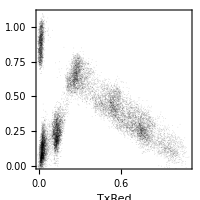

```mathematica
ListPlot[ToExpression["popt0"][[;;,1,{3,4}]]/5,PlotRange->{{0,1.1},{0,1.1}},AspectRatio->1,FrameStyle->Directive[{Black,12}],FrameLabel->{channelo,channelg},PlotRange->All,PlotStyle->Directive[{Opacity[0.2],Black}],ImageSize->200]
```

{RGBColor[0, 0, 0],RGBColor[0.3, 0, 0.63],RGBColor[0.76, 0, 0.5],RGBColor[1, 0.11, 0.35],RGBColor[1, 0.36, 0],RGBColor[1, 0.76, 0]}

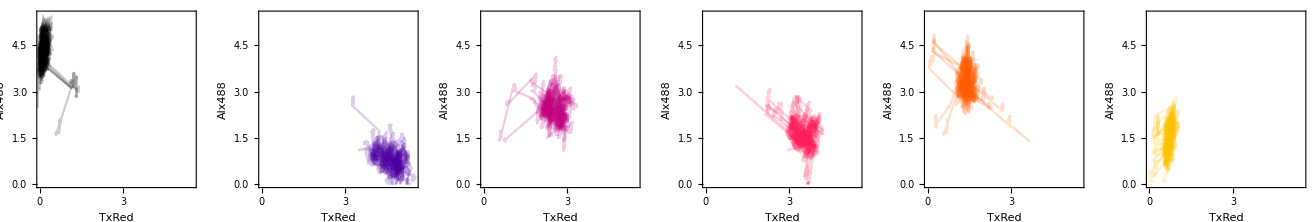

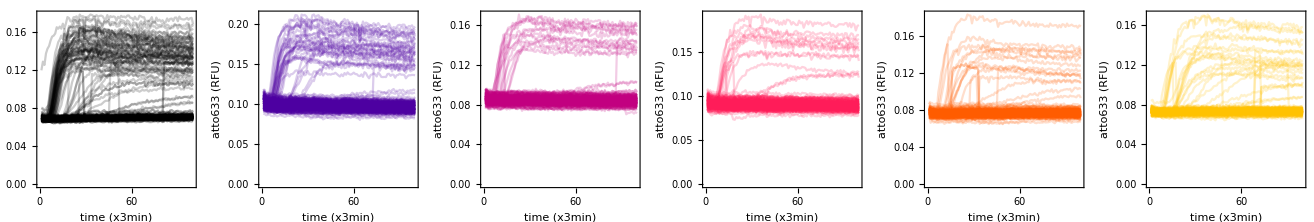

```mathematica
popcol={RGBColor[0,0,0],RGBColor[0.3,0,0.63],RGBColor[0.76,0,0.5],RGBColor[1,0.11,0.35],RGBColor[1,0.36,0],RGBColor[1,0.76,0]}(*colors assigned for each population*)
poptraj@trajall
dropletcount=Table[Length@ToExpression["popt"<>ToString[p]],{p,npop}];
Table[ListLinePlot[RandomSample[ToExpression["popt"<>ToString[p]][[;;,;;,{3,4}]],200],PlotRange->{{0,1.1*colorfact},{0,1.1*colorfact}},AspectRatio->1,FrameStyle->Directive[{Black,12}],FrameLabel->{channelo,channelg},PlotRange->All,PlotStyle->Directive[{Opacity[0.2],popcol[[p]]}],ImageSize->200],{p,npop}]//GraphicsRow
Table[ListLinePlot[RandomSample[ToExpression["popt"<>ToString[p]][[;;,;;,5]],200],AspectRatio->1,FrameStyle->Directive[{Black,12}],FrameLabel->{"time (x3min)","atto633 (RFU)"},PlotRange->All,PlotStyle->Directive[{Opacity[0.2],popcol[[p]]}],ImageSize->200],{p,npop}]//GraphicsRow
```

```mathematica
Subtraction of the baseline
```

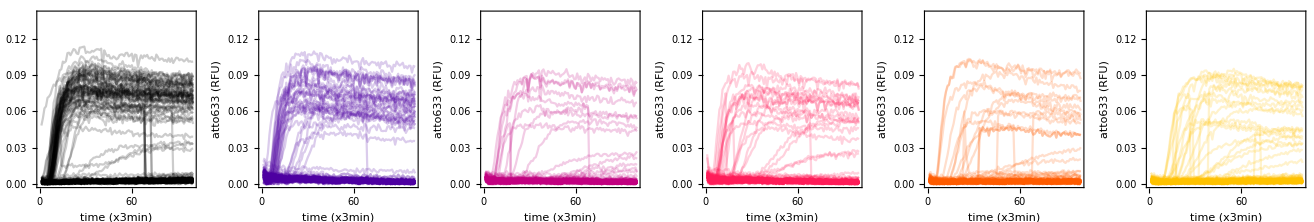

```mathematica
FctMin[list_]:=list-Min[list];
ttmin=Table[FctMin[#]&/@ToExpression["popt"<>ToString[p]][[;;,;;,5]],{p,npop}];
plotmin=Table[ListLinePlot[RandomSample[ttmin[[p]],200],FrameStyle->Directive[{Black,12}],AspectRatio->1,FrameLabel->{"time (x3min)","atto633 (RFU)"},PlotRange->{0,0.14},PlotStyle->Directive[{Opacity[0.2],popcol[[p]]}],ImageSize->200],{p,npop}]//GraphicsRow
```

```mathematica
Normalization
```

```mathematica
Table[Length@ToExpression["popt"<>ToString[p]],{p,npop}] (*number of droplets for each population*)
FctNormal[list_,thr_]:=list/If[Max[list]>thr,Max[list],0.1];thresr=0.025;
ttnormal=Table[FctNormal[MovingAverage[#,5],thresr]&/@ttmin[[p]],{p,npop}];
plotnormal=Table[ListLinePlot[RandomSample[ttnormal[[p]],200],FrameStyle->Directive[{Black,12}],AspectRatio->1,FrameLabel->{"time (x3min)","atto633 (normalized)"},PlotRange->{0,1.05},PlotStyle->Directive[{Opacity[0.2],popcol[[p]]}],ImageSize->200],{p,npop}]//GraphicsRow
```

{1703,788,1802,1884,1952,2439}

-Graphics-

```mathematica
Cleaning of the time traces
(*stop the time trace when large fluorescence jumps are observed*)
```

```mathematica
FctDeriv[timet_]:=Table[timet[[i+1]]-timet[[i]],{i,95}]
FindTrackStop[timet_]:=(n=1;While[-0.1<timet[[n+1]]<0.17,n++];n)
ttderiv=Table[FctDeriv[#]&/@ttnormal[[p]],{p,npop}];
plotderiv=Table[ListLinePlot[RandomSample[ttderiv[[p]],500],FrameStyle->Directive[{Black,12}],AspectRatio->1,FrameLabel->{"time (x3min)","atto633 (normalized)"},PlotRange->{-0.3,0.3},PlotStyle->Directive[{Opacity[0.2],popcol[[p]]}],ImageSize->200],{p,npop}]//GraphicsRow
stoptime=Table[FindTrackStop[#]&/@ttderiv[[p]],{p,npop}];
ttstop=Table[Table[ttnormal[[p,i,;;stoptime[[p,i]]]],{i,Length@ttnormal[[p]]}],{p,npop}];
Length[#]&/@ttstop
plotclean=Table[ListLinePlot[RandomSample[ttstop[[p]],500],FrameStyle->Directive[{Black,12}],AspectRatio->1,FrameLabel->{"time (x3min)","atto633 (normalized)"},PlotRange->{0,1.05},PlotStyle->Directive[{Opacity[0.2],popcol[[p]]}],ImageSize->200],{p,npop}]//GraphicsRow
```

-Graphics-

Part::partw: Part 96 of {-0.00281909,0.000171341,-0.00558894,-0.00180062,0.000427508,0.000532141,-0.00357879,0.00346024,-0.00116054,0.000558264,-0.00141615,0.00241571,-0.00379208,0.00241581,-0.00029691,0.000329841,«19»,-0.00210697,0.000552821,0.0000107452,-0.000155206,-0.00310199,0.00352413,-0.00159277,-0.00127864,0.000862441,0.00427578,0.000979801,-0.000718006,0.00552113,0.0157194,0.0165789,«45»} does not exist.

Part::partw: Part 96 of {-0.00671404,-0.000330247,-0.00403441,0.00283751,-0.000587549,0.00212282,0.00101628,0.00101283,-0.00389066,-0.000160799,0.0240338,0.0203524,0.0209804,0.0229835,0.0237275,-0.00234025,«19»,0.00355987,-0.0000529156,0.00220817,0.000348461,-0.00124293,-0.0000732609,-0.00283296,0.00126744,0.000483436,-0.00196154,-0.00146503,-0.000748991,0.000600796,0.00127241,0.00487507,«45»} does not exist.

Part::partw: Part 96 of {-0.00243732,-0.00283454,-0.00321927,-0.000405014,0.0018024,-0.000803897,0.00147942,0.00203693,-0.00075284,-0.000130686,0.00348504,-0.00133937,-0.00139075,0.00481546,-0.00106833,-0.0026447,«19»,0.00180563,0.000403217,0.000898279,-0.00036368,-0.00319346,0.000377103,-0.0000441697,-0.00181442,-0.000568763,0.000411566,0.000574321,-0.00171172,0.00382901,0.00512427,0.00018243,«45»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{1703,788,1802,1884,1952,2439}

-Graphics-

```mathematica
Extraction of the amplification times and plot of the distributions
```

```mathematica
FindCt[timet_,tres_]:=If[Max[timet]>tres,(n=1;While[timet[[n]]<tres,n++];n),96];
thresholdAtto633=0.3;
atpop=Table[FindCt[#,thresholdAtto633]&/@ttstop[[p]],{p,npop}];
startercount=Length@#&/@Table[Select[atpop[[p]],#<96&],{p,npop}];
atdistrib=Table[Table[Count[atpop[[p]],u_/;u<t],{t,96}],{p,npop}];
atfreq2=Table[#/Length@atpop[[p]]&/@Table[Count[atpop[[p]],u_/;u=t],{t,96}],{p,npop}];
atfreq=Table[#/Length@atpop[[p]]&/@Table[Count[atpop[[p]],u_/;u<t],{t,96}],{p,npop}];
timeframe=Table[3i,{i,Length@atfreq[[1]]}];
```

Set::nosym: u_/;u does not contain a symbol to attach a rule to.

General::stop: Further output of Set::nosym will be suppressed during this calculation.

```mathematica
Grid[{Prepend[samplename, "sample"],Prepend[dropletcount, "droplet count"],Prepend[startercount, "starter count"]},Frame->All]
```

sample | 0% H2O2 | 0.3% | 0.6% | 1.3% | 2.5% | 5%
droplet count | 1703 | 788 | 1802 | 1884 | 1952 | 2439
starter count | 472 | 108 | 169 | 160 | 119 | 206

-Graphics-

-Graphics-

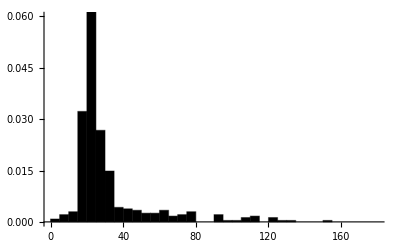
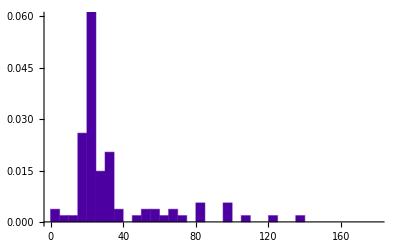
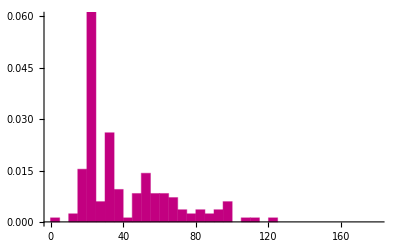
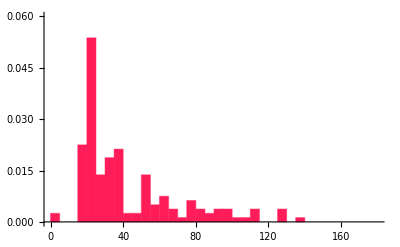
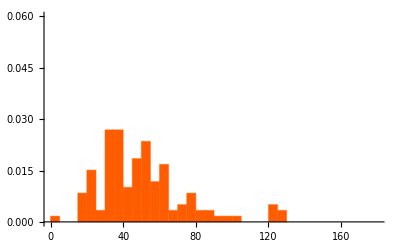
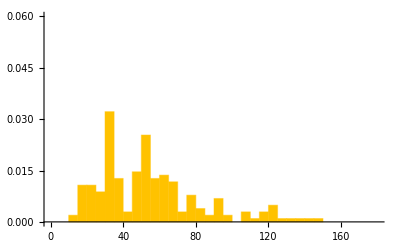

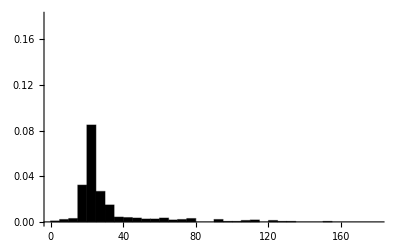
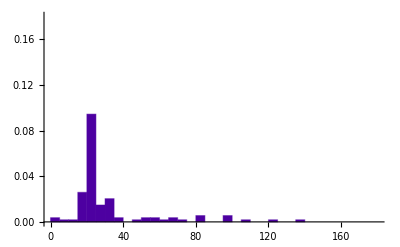

```mathematica
axsty={Directive[{Black,16}],Directive[{Opacity[0],White,16}],Directive[{Opacity[0],White,16}],Directive[{Opacity[0],White,16}],Directive[{Opacity[0],White,16}],Directive[{Opacity[0],White,16}]};
title={"Activity Distribution (inlcuding non starting droplets","","","","","",""};
test=Table[Show[Graphics[ListLinePlot[Transpose[{timeframe,atfreq2[[p]]}],PlotLabel->title[[p]],Axes->True,AxesStyle->axsty[[p]],PlotRange->{{0,200},{0,0.07}},Frame->None,InterpolationOrder->0,PlotStyle->popcol[[p]],Filling->Axis,ImageSize->500]]],{p,6}];
outlineplot=Graphics[Table[{Inset[test[[i]],Offset[{20i,25i},{0,0}]]},{i,6}],ImageSize->800]
hist=Table[HistogramList[3*atpop[[p]],{0,180,6},"PDF"],{p,6}];
hist2={#[[1]],Append[#[[2]],0]}&/@hist;title={"Activity Distribution of starting droplets","","","","","",""};test=Table[Show[Graphics[ListLinePlot[Transpose[hist2[[p]]],Axes->True,PlotLabel->title[[p]],AxesStyle->axsty[[p]],PlotRange->{0,0.07},Frame->None,InterpolationOrder->0,PlotStyle->popcol[[p]],Filling->Axis,ImageSize->500]]],{p,6}];
outlineplot=Graphics[Table[{Inset[test[[i]],Offset[{20i,25i},{0,0}]]},{i,6}],ImageSize->800]
range={{0,0.06},{0,0.06},{0,0.06},{0,0.06},{0,0.06},{0,0.06}};
Table[Histogram[3*atpop[[p]],{0,180,5},"PDF",PlotRange->range[[p]],AxesStyle->Directive[{Black,12}],ChartStyle->Directive[{EdgeForm->None,popcol[[p]]}]],{p,npop}]
Table[Histogram[3*Select[atpop[[p]],#<90&],{0,180,5},"PDF",PlotRange->{0,0.18},AxesStyle->Directive[{Black,12}],ChartStyle->Directive[{EdgeForm->None,popcol[[p]]}]],{p,npop}]
```